# 1. 简介

## -Graphics-

## -Graphics-

# 2. 常用数学软件

1. Mathematica 综合-全能(符号演算)
2. MatLab      综合-全能(数值计算)
3. Lingo       数学规划类(专业工具)
4. SPSS        中小型统计分析

# 3. 导言

## 3.1 丰富的内部函数--书写规则及格式要求

1. [] --函数专用
2. () --用户专用
3. {} --列表专用

## 3.2 Introduction 引言 --- 基本功能简介

3.2.1 变量赋值

```mathematica
rent = 350
food = 175
heat = 83
rent + food + heat
```

350

175

83

608

3.2.2 调用函数

```mathematica
Factor[x^5-1] (*因式分解*)
Factor[x-1]
```

(-1+x) (1+x+x^2+x^3+x^4)

-1+x

```mathematica
Sovle[x^3 - 2 x + 1 == 0, x] (*解方程*) (*对x变量*)

(*求积分*)
Integrate[1/(1 - x^3), x] (*x不带范围为求不定积分*)
Integrate[x^2.5 - 5.0911x, {x, 0, 20}] (*x带范围,则为求定积分 *)
```

Sovle[1-2 x+x^3==0,x]

ArcTan[(1+2 x)/(√3)]/(√3)-1/3 Log[1-x]+1/6 Log[1+x+x^2]

9203.81

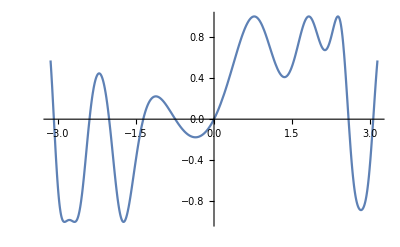

```mathematica
Plot[Sin[x + Sqrt[2] Sin[x^2]], {x, -Pi, Pi}]
```

```mathematica
2^64
```

18446744073709551616

```mathematica
% (*输出上一个out结果*)
Out[1] (*输出第一个结果*)
%6 (*输出第六个结果*)
```

18446744073709551616

350

-1+x

3.2.3 自定义函数

```mathematica
BowlingScore[pins_] := Module[{score}, (*注意pins_的_*)
    score[{x_, y_, z_}] := x + y + z;
    score[{10, y_, z_, r___}] := 10+y+z+score[{y, z, r}];
    score[{x_, y_, z_, r___}] := x+y+z+score[{z, r}] /;
                                 x + y == 10;
    score[{x_, y_, r___}] := x+y+score[{r}] /; x+y < 10;
    score[
    If[pins[[-2]] + pins[[-1]] >= 10, pins,
            Append[pins, 0]]]
            ]
BowlingScore[{10, 10, 10, 10, 10, 10, 10, 10, 10, 10, 10, 10}]
```

300

```mathematica
fib[n_]:=
Module[{f},
 f[1] = f[2]=1;
 f[i_]:=f[i]=f[i-1]+f[i-2];
 f[n]
]
fib[10]
gcd[m0_,n0_]:=
Module[{m=m0,n=n0},
While[n≠0,{m,n}={n,Mod[m,n]}];
m
]
gcd[18,21]
```

55

3

# 4. Using Mathematica 使用

## 4.1 Getting Into and Out of Mathematica 进入和推出 4.2 Getting Help 获得帮助

```mathematica
?ParametricPlot
```

```mathematica
?Int*
```

## 4.3 The Syntax of Inputs 输入的句法

```mathematica
39/13
2^5
25*4
25 4
```

3

32

100

100

```mathematica
x = 4
y = 2
z = 5
y z
25 x
Clear[x] (*清除*)
```

4

2

5

10

100

3-4 ⅈ

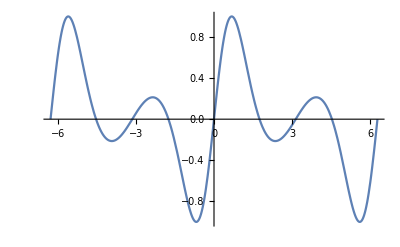

```mathematica
Conjugate[3+4 I] (*给出复数 z 的复共轭.*)
Plot[Sin[x + Sqrt[2] Sin[x]], {x, -2Pi, 2Pi}]
```

```mathematica
Clear@x (*!清除x的赋值*)
Integrate[Cos[x],{x,a,b}]
∫Cos[x]ⅆx
```

-Sin[a]+Sin[b]

Sin[x]

```mathematica
x = Range[100];
Apply[Plus,x] (*将Plus应用于x*)
% / 100
?x
```

5050

101/2

```mathematica
Clear[x]
D[Sin[x],        (* differentiate Sin[x]   *) 
       {x, 2}]   (* with respect to x once *)
```

-Sin[x]

```mathematica
Clear@x(*!清除x的赋值*)
 x^5 - 1  //Factor (*后缀法,有点问题*)
```

(-1+x) (1+x+x^2+x^3+x^4)

## 4.4 Errors 出错信息